# Homework 2

Wang Long 1101110160

## Data generation

Simulated Data for 3 models. Fitting the velocity by Sin function.

```mathematica
Needs["PlotLegends`"]
Off[RandomVariate::realprm]
Off[NonlinearModelFit::cvmit]
Off[NonlinearModelFit::eit]
Off[FittedModel::constr]
(*Random(Subscript[ϕ, s],Subscript[r, s])*)
datalist1=Table[{2π*RandomReal[],5*Sqrt@RandomReal[]},{i,10000}];
(*x,y,Subscript[ϕ, s],Subscript[r, s]*)
datalist2=Cases[datalist1,{phi0_,r0_}->{r0*Cos[phi0],r0*Sin[phi0],phi0,r0}];
(*phi0,r0,phic,rc*)
datalist3=Cases[datalist2,{x_,y_,phi0_,r0_}->{phi0,r0,ArcTan[y/(8.5-x)],Sqrt[(8.5-x)^2+y^2]}];
vc=220;
σr=20;
σϕ=10;
fun1[ϕ_]:=Flatten@Transpose@(Table[vc{Cos[#],Sin[#]}&@ϕ-(RandomVariate[NormalDistribution[0,#]]&/@{σϕ,σr}),{i,3}])
fun2[rc_,phi0_,phic_]:=Flatten@((vc{1,1/8.5*rc,1*Sqrt[8.5/rc]}*#)&/@{Cos[phi0+phic],Sin[phi0+phic](*,-y/rc,Abs[x-8.5]/rc*)})
(*phi0,r0,phic,rc,vphi0(1,2,3),vr0(1,2,3)*)
datalist4=Table[datalist3[[i]]~Join~(fun2@@datalist3[[i,{4,1,3}]]-fun1[datalist3[[i,1]]]),{i,Length@datalist3}];
(*phi0,r0,phic,rc,vphi0(1,2,3)/r0,vr0(1,2,3)/r0*)
datalist5=Cases[datalist4,{phi0_,r0_,phic_,rc_,vp1_,vp2_,vp3_,vr1_,vr2_,vr3_}->{phi0,r0,phic,rc}~Join~({vp1,vp2,vp3,vr1,vr2,vr3}/r0)];
(*Fit*)
datafitlist=Table[NonlinearModelFit[(Sort[Select[datalist5,2i-2≤#[[2]]≤4i-3&],#1[[1]]<#2[[1]]&])[[All,{1,j}]],{A Sin[w x+ϕ0]+B,A>0,1<w<3},{A,B,ϕ0,{w,2}},x],{i,{1,2}},{j,5,10}];
(*Label defination*)
vlabel={"v_ϕ(model1)","v_ϕ(model2)","v_ϕ(model3)","v_r(model1)","v_r(model2)","v_r(model3)"};
dlabel={"(r≤1kpc)","(r≥2kpc)"};
```

## Save data

```mathematica
Save["/Users/wanglong/Dropbox/Writing/lessons/dynamics/Homework2dat","`*"]
```

```mathematica
Get["/Users/wanglong/Dropbox/Writing/lessons/dynamics/Homework2dat"];
```

## Plot

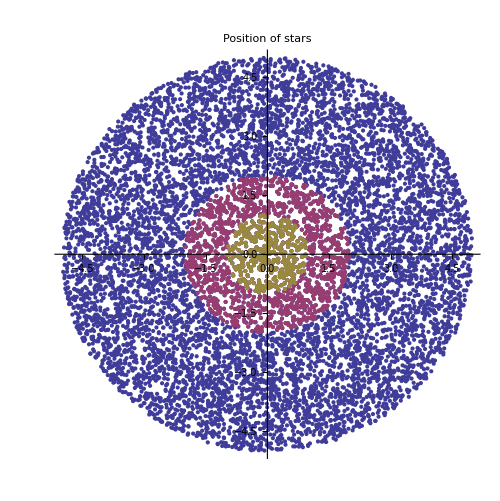

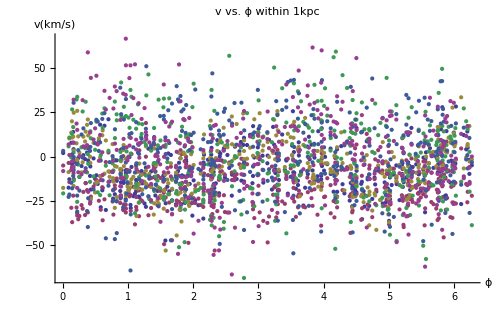

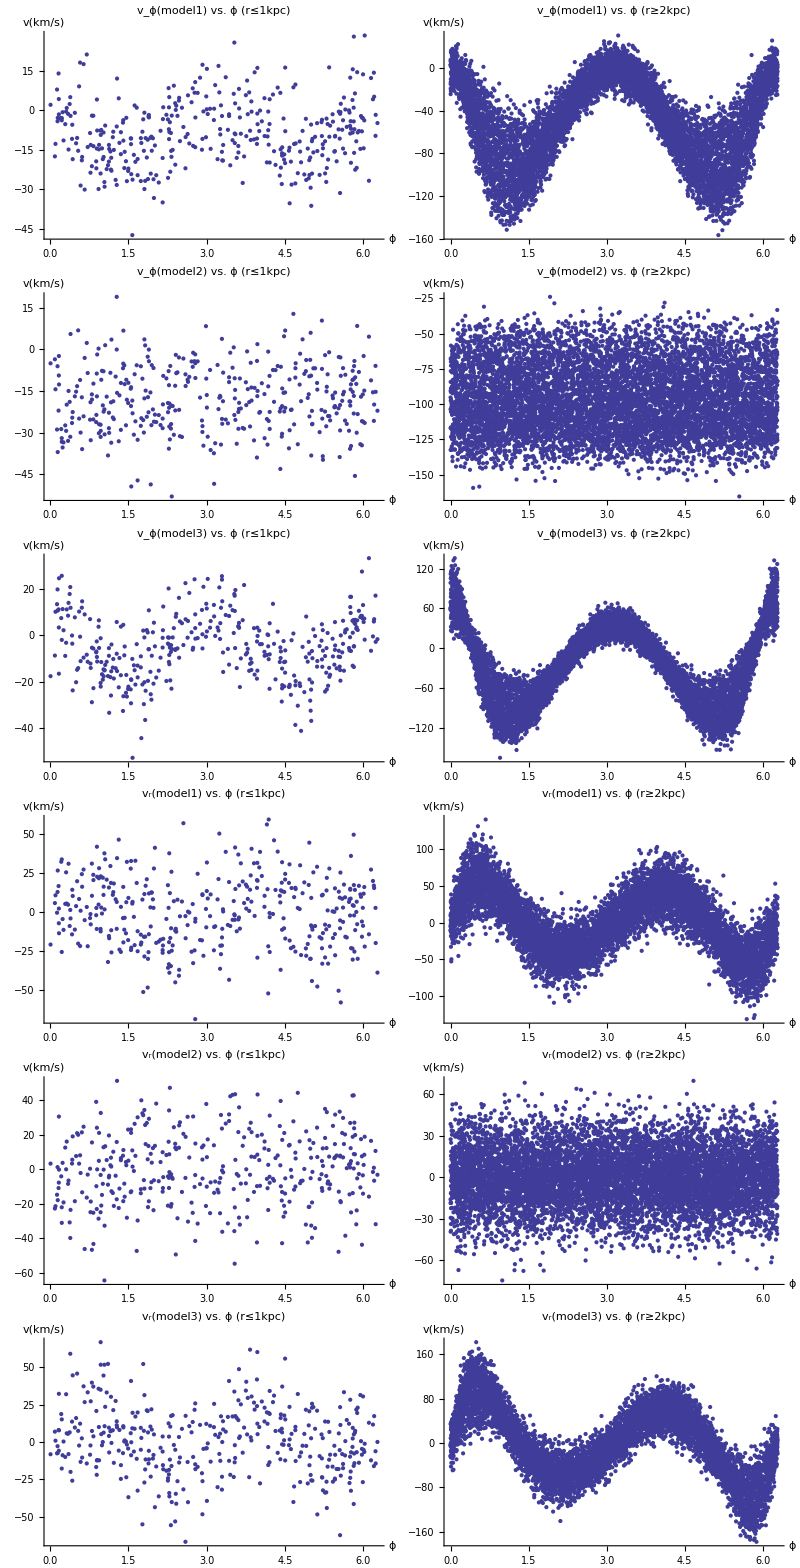

Fit of v_ϕ/r_s vs. ϕ

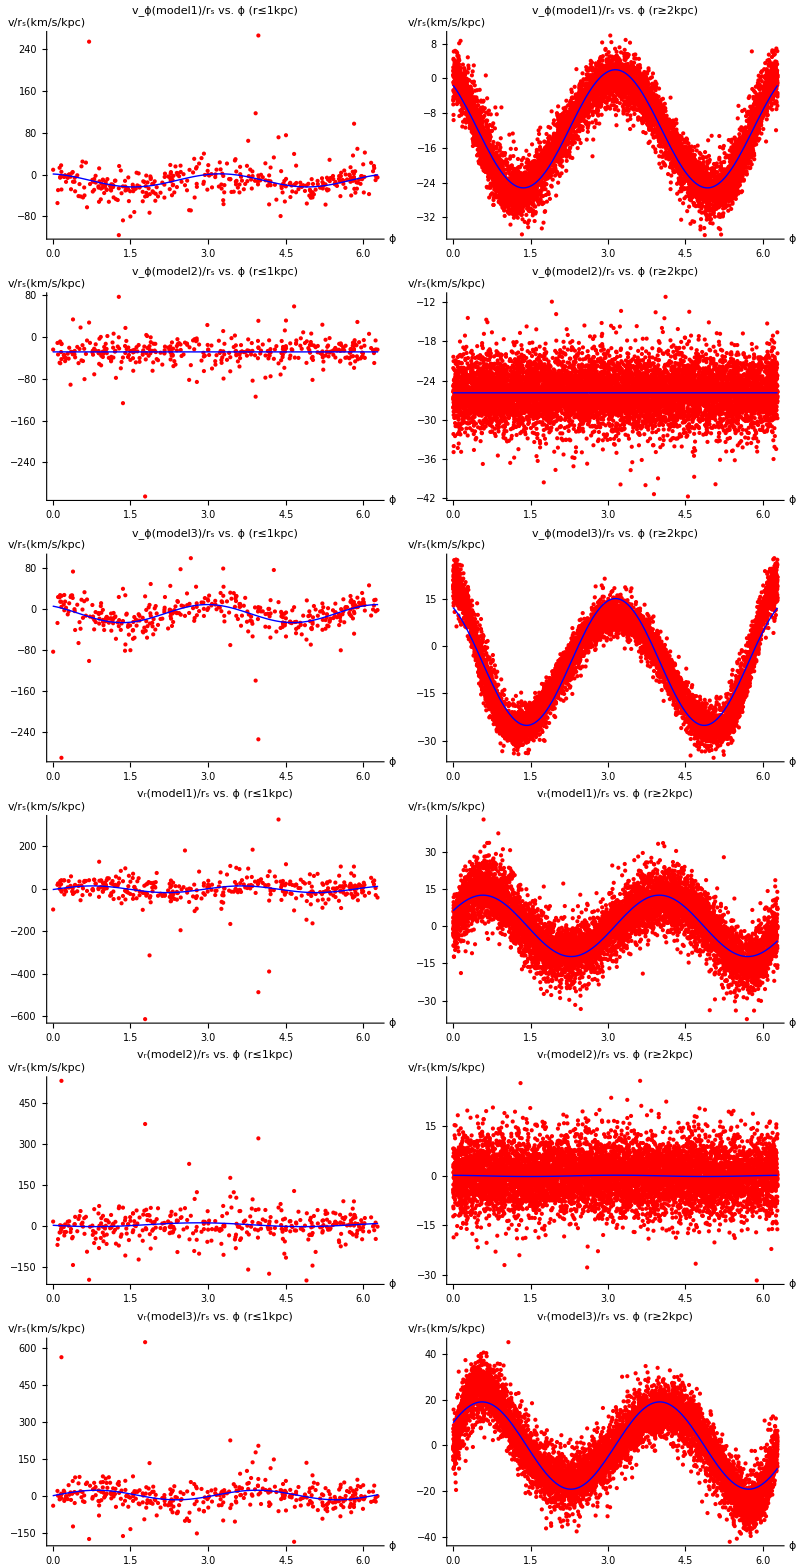

Table of fitting parameters

r | model | Pars | Estimate | Standard Error | t-Statistic | P-Value
(r≤1kpc) | Model1 | A | 12.5381 | 2.35307 | 5.3284 | 1.70393×10^-7
(r≥2kpc) | Model1 | A | 13.5821 | 0.0570759 | 237.966 | 6.4285313372×10^-3742
(r≤1kpc) | Model2 | A | 5.86338×10^-13 | 1.87598 | 3.1255×10^-13 | 1
(r≥2kpc) | Model2 | A | 3.88899×10^-10 | 0.0467728 | 8.31463×10^-9 | 1
(r≤1kpc) | Model3 | A | 17.6244 | 2.34569 | 7.51352 | 4.18188×10^-13
(r≥2kpc) | Model3 | A | 20.0821 | 0.0833169 | 241.033 | 9.0571717312×10^-3783
(r≤1kpc) | Model1 | B | -10.9163 | 1.74275 | -6.26385 | 1.02003×10^-9
(r≥2kpc) | Model1 | B | -11.6033 | 0.0410504 | -282.661 | 2.615641468×10^-4301
(r≤1kpc) | Model2 | B | -28.2512 | 1.33034 | -21.2361 | 1.71183×10^-66
(r≥2kpc) | Model2 | B | -25.86 | 0.0331403 | -780.318 | 3.9228348855×10^-7858
(r≤1kpc) | Model3 | B | -8.7264 | 1.73836 | -5.01991 | 7.96989×10^-7
(r≥2kpc) | Model3 | B | -5.10094 | 0.0609237 | -83.7267 | 3.1883979243×10^-1110

```mathematica
(*Position distribution*)
ListPolarPlot[Table[Select[datalist5,#[[2]]≤i&][[All,1;;2]],{i,{5,2,1}}],PlotLabel->"Position of stars",AxesLabel->{"r(kpc)"},PlotStyle->Automatic,PlotLegend->{"r≤5kpc","r≤2kpc","r≤1kpc"},LegendPosition->{1,0},LegendSize->{0.4,0.4},LegendShadow->None,ImageSize->500]
(*All data v/Subscript[r, s] vs. ϕ*)
Plotrange=5;
ListPlot[Table[(Sort[Select[datalist4,#[[2]]≤1&],#1[[1]]<#2[[1]]&])[[All,{1,i}]],{i,5,5+Plotrange,1}],Joined->False,PlotLegend->vlabel[[1;;Plotrange+1]],LegendPosition->{1,0},LegendSize->{0.4,0.4},ImageSize->500,PlotLabel->"v vs. ϕ within 1kpc",AxesLabel->{"ϕ","v(km/s)"},LegendShadow->None]
Grid[Transpose@Table[ListPlot[(Sort[Select[datalist4,2i-2≤#[[2]]≤4i-3&],#1[[1]]<#2[[1]]&])[[All,{1,j}]],PlotRange->Automatic,PlotLabel->vlabel[[j-4]]<>" vs. ϕ "<>dlabel[[i]],AxesLabel->{"ϕ","v(km/s)"},ImageSize->250],{i,{1,2}},{j,5,10}]]
(*Fit data of v vs. ϕ*)
"Fit of v_ϕ/r_s vs. ϕ"
Grid[Transpose@Table[ListPlot[(Sort[Select[datalist5,2i-2≤#[[2]]≤4i-3&],#1[[1]]<#2[[1]]&])[[All,{1,j}]],PlotStyle->Red,PlotRange->Automatic,Epilog->First@Plot[datafitlist[[i,j-4]][x],{x,0,2π},PlotStyle->Blue],PlotLabel->vlabel[[j-4]]<>"/r_s vs. ϕ "<>dlabel[[i]],AxesLabel->{"ϕ","v/r_s(km/s/kpc)"},ImageSize->250],{i,{1,2}},{j,5,10}]]
(*A,B*)
"Table of fitting parameters"
Grid[{Flatten@Prepend[datafitlist[[1,1]]["ParameterTable"][[1,1,1,2;;]],{"r","model","Pars"}]}~Join~Flatten[Table[Flatten@{dlabel[[i]],"Model"<>ToString@j,datafitlist[[i,j]]["ParameterTable"][[1,1,1+m]]},{m,2},{j,3},{i,2}],2],Frame->All]
```

## Discussion

### f:

The difference between r≤1kpc and r≥2kpc is not obvious. The result of A and B is similar for model1 and model2.

### e:

The Oort’s constant A represents the shear of the rotation. For model 1 all stars have same rotation velocity, so stars at different distance respect to galaxy center will have shear of the angular rotation velocity ω and A will not be zero. For model 2 v∝r, so ω is same for all stars. There is no shear of ω thus A is zero. Model 3 v∝r^(-1/2), star at larger distance will have slower rotation velocity so A is larger than model 1’s. 

The Oort’s constant B represents the vorticity of the velocity field, in other word, represents the surrounding stars’ rotation velocity respect to the sun (κ_0^2=-4 Bω_0). For model 1, stars around sun will have rotation respect to sun, so B is less than zero. For model 2, since stars at larger distance than sun have larger rotation velocity than model 1’s, so the rotation respect to sun is even larger thus B is less than model 1’s. For model 3, stars at larger distance have slower rotation velocity, so their rotation velocity respect to sun is slower than model 1’s, which result in larger B. 

The observation of A and B is consistent with model 1 which means the stars around suns have same rotation velocity.

## Code Backup

```mathematica
(*Random(x,y)*)
(*datalist1=RandomReal[{-1,1},{10000,2}];*)
(*x,y,r0*)
(*datalist2=(Sort[{#1,#2,Sqrt[#1^2+#2^2]}&@@@datalist1,#1[[3]]<#2[[3]]&])[[;;5000]];*)
(*x,y,phi0,r0,phic,rc*)
(*datalist3=Cases[datalist2/datalist2[[Length@datalist2,3]]*5,{x_,y_,z_}->{x,y,Piecewise[{{ArcCos[x(x^2+y^2)^(-1/2)],y≥0},{2π-ArcCos[x(x^2+y^2)^(-1/2)],y<0}}],z,ArcTan[-y/(x-8.5)],Sqrt[(x-8.5)^2+y^2]}];*)
```

```mathematica
(*Cases[datalist3,{x_,y_,phi0_,r0_,phic_,rc_}->{phi0,r0,phic,rc}~Join~(Flatten@((vc{1,1/8.5*rc,1*Sqrt[8.5/rc]}*#)&/@{Cos[phi0+phic],Sin[phi0+phic](*,-y/rc,Abs[x-8.5]/rc*)})-fun1[phi0])];*)
```